```mathematica
rmax=10.0;dr=0.1;
```

```mathematica
rlist=Range[-rmax,rmax,dr]
```

{-10.,-9.9,-9.8,-9.7,-9.6,-9.5,-9.4,-9.3,-9.2,-9.1,-9.,-8.9,-8.8,-8.7,-8.6,-8.5,-8.4,-8.3,-8.2,-8.1,-8.,-7.9,-7.8,-7.7,-7.6,-7.5,-7.4,-7.3,-7.2,-7.1,-7.,-6.9,-6.8,-6.7,-6.6,-6.5,-6.4,-6.3,-6.2,-6.1,-6.,-5.9,-5.8,-5.7,-5.6,-5.5,-5.4,-5.3,-5.2,-5.1,-5.,-4.9,-4.8,-4.7,-4.6,-4.5,-4.4,-4.3,-4.2,-4.1,-4.,-3.9,-3.8,-3.7,-3.6,-3.5,-3.4,-3.3,-3.2,-3.1,-3.,-2.9,-2.8,-2.7,-2.6,-2.5,-2.4,-2.3,-2.2,-2.1,-2.,-1.9,-1.8,-1.7,-1.6,-1.5,-1.4,-1.3,-1.2,-1.1,-1.,-0.9,-0.8,-0.7,-0.6,-0.5,-0.4,-0.3,-0.2,-0.1,0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.,3.1,3.2,3.3,3.4,3.5,3.6,3.7,3.8,3.9,4.,4.1,4.2,4.3,4.4,4.5,4.6,4.7,4.8,4.9,5.,5.1,5.2,5.3,5.4,5.5,5.6,5.7,5.8,5.9,6.,6.1,6.2,6.3,6.4,6.5,6.6,6.7,6.8,6.9,7.,7.1,7.2,7.3,7.4,7.5,7.6,7.7,7.8,7.9,8.,8.1,8.2,8.3,8.4,8.5,8.6,8.7,8.8,8.9,9.,9.1,9.2,9.3,9.4,9.5,9.6,9.7,9.8,9.9,10.}

```mathematica
n=Length[rlist]
```

201

```mathematica
V[r_]:=r^2;
```

```mathematica
V1=Table[If[Abs[r]≤5,0,1],{r,Range[-rmax,rmax,dr]}];
```

```mathematica
Vmat=DiagonalMatrix[V[rlist]];
```

```mathematica
ListDensityPlot[Vmat]
```

-Graphics-

```mathematica
(*calculate KE matrix*)
one[n_,d_]:=
DiagonalMatrix[1+0Range[n-Abs[d]],d];
KE=-1/2 1/dr^2(one[n,-1]-2 one[n,0]+one[n,1]);
```

```mathematica
H=KE+Vmat;
```

```mathematica
{eval,evec}=Eigensystem[H];
```

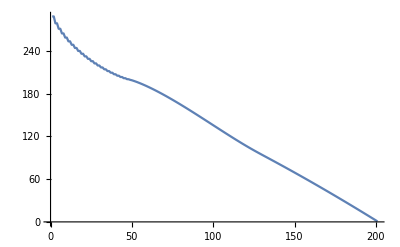

```mathematica
ListLinePlot[eval]
```

```mathematica
eval[[201]]
```

0.706481

```mathematica
Manipulate[ListPlot[{rlist,evec⟦-i⟧}ᵀ,Joined->True,PlotRange->All],{i,1,n,1}]
```